Homework 4 Code - Be sure to change the axis names at the very end of this document.

```mathematica
(*Data is Entered Here*)
xdata={};
ydata={};
ErrorData={};

(*NO NEED TO ALTER THE REMAINING CODE*)











Needs["ErrorBarPlots`"]

(*Converting the ydata and combining the previous lists*)
L=Length[xdata];
ϵ=Mean[xdata]/6;
xmin=Min[xdata]-ϵ;
xmax=Max[xdata]+ϵ;
ylogdata=ydata//N;
xylogdata=Thread[{xdata,ylogdata}];
ErrorData2=ErrorData;
ErrorData3=Table[ErrorBar[ErrorData2[[i]]],{i,1,L}];
xylogErrordata=Thread[{xylogdata,ErrorData3}];
```

Here the least squares-fit is made according to the linfit program procedure. (Courtesy of David Wynne)

```mathematica
Δ=L*∑_(i=1)^L (xdata[[i]])^2-(∑_(i=1)^L xdata[[i]])^2
```

336

Δ is a parameter needed for calculations below:

```mathematica
m=1/Δ(L*∑_(i=1)^L (xdata[[i]]*ylogdata[[i]])-(∑_(i=1)^L xdata[[i]])*∑_(i=1)^L ylogdata[[i]])
```

-0.283307

m is the slope of the best-fit line.

```mathematica
b=1/Δ((∑_(i=1)^L (xdata[[i]])^2*∑_(i=1)^L ylogdata[[i]])-(∑_(i=1)^L xdata[[i]])*(∑_(i=1)^L (xdata[[i]]*ylogdata[[i]])))
```

6.88841

b is the intercept of the best-fit line.

```mathematica
σy=√(1/(L-2)*∑_(i=1)^L (ylogdata[[i]]-(m*xdata[[i]]+b))^2)
```

0.0400282

σy is the standard deviation of the difference between the measured y and the predicted y (=mx+b).

```mathematica
δm=√((L*σy^2)/Δ)
```

0.00617648

δm is the uncertainty in the slope

```mathematica
δb=√((σy^2*∑_(i=1)^L (xdata[[i]])^2)/Δ)
```

0.0258381

Summary:

```mathematica
Grid[{{"m",m},{"δm",δm},{"b",b},{"δb",δb}},Frame->All] (*Run this!*)
```

m | -0.283307
δm | 0.00617648
b | 6.88841
δb | 0.0258381

Check the graph:

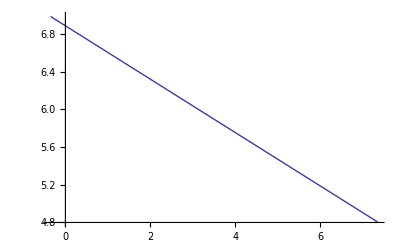

```mathematica
f[X_]:=m*X+b
p2=Plot[f[X],{X, xmin,xmax}]
```

Now that the data has been fit according to a least squares fit procedure we will make the error bar plot. This will yield a plot with both the list plot with error bars and the best fit curve. If desired, change the FrameLable and PlotLabel arguements if you want different labels for your plot.

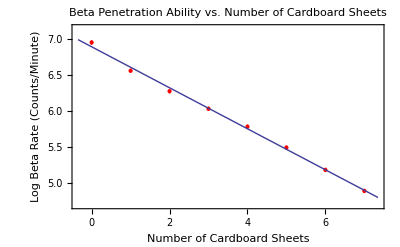

```mathematica
ϵ2=ϵ=Mean[ylogdata]/30;
ymin=Min[ylogdata]-ϵ2;
ymax=Max[ylogdata]+ϵ2;

p1=ErrorListPlot[xylogErrordata,PlotStyle->{Red,PointSize[Small]},PlotRange->{{xmin,xmax},All}];
Show[p1,p2,Frame->True,Axes->False,LabelStyle->{FontFamily->"Times",FontSize->13},FrameLabel->{"Number of Cardboard Sheets","Log Beta Rate (Counts/Minute)"},PlotLabel->"Beta Penetration Ability vs. Number of Cardboard Sheets",FrameStyle->Thickness[0.0027],PlotRange->{ymin,ymax}]
```